```mathematica
Binomial[n-4,2]
```

1/2 (-5+n) (-4+n)

```mathematica
Binomial[n-4,2]* 4*x+2*(n-4)*4*y+2*(n-4)*(n-2)*x+4*(n-2)*y+4*z+2*(n-2)*x
```

2 (-5+n) (-4+n) x+2 (-2+n) x+2 (-4+n) (-2+n) x+8 (-4+n) y+4 (-2+n) y+4 z

```mathematica
Simplify[2 (-5+n) (-4+n) x+2 (-2+n) x+2 (-4+n) (-2+n) x+8 (-4+n) y+4 (-2+n) y+4 z]
```

4 ((13-7 n+n^2) x+(-10+3 n) y+z)

```mathematica
Binomial[n-3,2]xy
```

1/2 (-4+n) (-3+n) xy

```mathematica
Binomial[n-3,2]*4*x+(n-3)*4*y+(n-3)(n-2)x+(n-2)y+(n-3)(n-2)y+(n-2)z+2(n-2)y
```

2 (-4+n) (-3+n) x+(-3+n) (-2+n) x+4 (-3+n) y+3 (-2+n) y+(-3+n) (-2+n) y+(-2+n) z

```mathematica
Simplify[2 (-4+n) (-3+n) x+(-3+n) (-2+n) x+4 (-3+n) y+3 (-2+n) y+(-3+n) (-2+n) y+(-2+n) z]
```

(30-19 n+3 n^2) x+(-12+2 n+n^2) y+(-2+n) z

```mathematica
Binomial[n-2,2]*4x+2(n-2)(n-2)y+2(n-2)z
```

2 (-3+n) (-2+n) x+2 (-2+n)^2 y+2 (-2+n) z

```mathematica
Simplify[2 (-3+n) (-2+n) x+2 (-2+n)^2 y+2 (-2+n) z]
```

2 (-2+n) ((-3+n) x+(-2+n) y+z)

```mathematica
Expand[2 (-2+n) ((-3+n) x+(-2+n) y+z)]
```

12 x-10 n x+2 n^2 x+8 y-8 n y+2 n^2 y-4 z+2 n z

```mathematica
Simplify[12 x-10 n x+2 n^2 x+8 y-8 n y+2 n^2 y-4 z+2 n z]
```

2 (-2+n) ((-3+n) x+(-2+n) y+z)

```mathematica
2 (-2+n) ((-3+n) x+(-2+n) y+z)+1
```

1+2 (-2+n) ((-3+n) x+(-2+n) y+z)

```mathematica
Expand[1+2 (-2+n) ((-3+n) x+(-2+n) y+z)]
```

1+12 x-10 n x+2 n^2 x+8 y-8 n y+2 n^2 y-4 z+2 n z

```mathematica
Simplify[1+12 x-10 n x+2 n^2 x+8 y-8 n y+2 n^2 y-4 z+2 n z]
```

1+2 (6-5 n+n^2) x+2 (-2+n)^2 y-4 z+2 n z

```mathematica
M={{n^2-7n+13,3n-10,1},{3n^2-19n+30,n^2+2n-12,n-2},
{2n^2-10+12,2n^2-8n+8,2n-4}}
```

{{13-7 n+n^2,-10+3 n,1},{30-19 n+3 n^2,-12+2 n+n^2,-2+n},{2+2 n^2,8-8 n+2 n^2,-4+2 n}}

```mathematica
Det[M]
```

-64+116 n+8 n^2-28 n^3+4 n^4

```mathematica
Simplify[-64+116 n+8 n^2-28 n^3+4 n^4]
```

4 (-16+29 n+2 n^2-7 n^3+n^4)

```mathematica
O={{0,3n-10,1},{0,n^2+2n-12,n-2},
{1,2n^2-8n+8,2n-4}}
```

Set::wrsym: Symbol O is Protected.

{{0,-10+3 n,1},{0,-12+2 n+n^2,-2+n},{1,8-8 n+2 n^2,-4+2 n}}

```mathematica
M1={{0,-10+3 n,1},{0,-12+2 n+n^2,-2+n},{1,8-8 n+2 n^2,-4+2 n}}
```

{{0,-10+3 n,1},{0,-12+2 n+n^2,-2+n},{1,8-8 n+2 n^2,-4+2 n}}

```mathematica
Det[M1]/Det[M]
```

(32-18 n+2 n^2)/(-64+116 n+8 n^2-28 n^3+4 n^4)

```mathematica
Simplify[(32-18 n+2 n^2)/(-64+116 n+8 n^2-28 n^3+4 n^4)]
```

(16-9 n+n^2)/(2 (-16+29 n+2 n^2-7 n^3+n^4))

```mathematica
M2={{n^2-7n+13,0,1},{3n^2-19n+30,0,n-2},
{2n^2-10+12,1,2n-4}}
```

{{13-7 n+n^2,0,1},{30-19 n+3 n^2,0,-2+n},{2+2 n^2,1,-4+2 n}}

```mathematica
Det[M2]/Det[M]
```

(56-46 n+12 n^2-n^3)/(-64+116 n+8 n^2-28 n^3+4 n^4)

```mathematica
Simplify[(56-46 n+12 n^2-n^3)/(-64+116 n+8 n^2-28 n^3+4 n^4)]
```

-(-56+46 n-12 n^2+n^3)/(4 (-16+29 n+2 n^2-7 n^3+n^4))

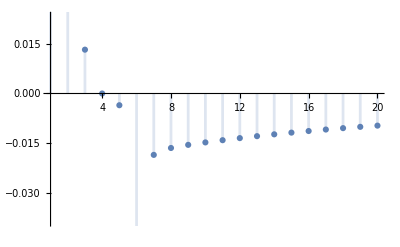

```mathematica
DiscretePlot[-(-56+46 n-12 n^2+n^3)/(4 (-16+29 n+2 n^2-7 n^3+n^4)),{n,1,20}]
```

```mathematica
M3={{n^2-7n+13,3n-10,0},{3n^2-19n+30,n^2+2n-12,0},
{2n^2-10+12,2n^2-8n+8,1}}
```

{{13-7 n+n^2,-10+3 n,0},{30-19 n+3 n^2,-12+2 n+n^2,0},{2+2 n^2,8-8 n+2 n^2,1}}

```mathematica
Det[M3]/Det[M]
```

(144-170 n+74 n^2-14 n^3+n^4)/(-64+116 n+8 n^2-28 n^3+4 n^4)